I was confused about the E scaling in the t-channel diagram for the VBS process and I was wondering where the E^3 comes from.

Naive counting is E^5/Q^2; however the SM vertex shouldn’t give you E^3 as it is a unitarized process; Upon minimizing Q^2 in the forward limit, which is allowed phase space configuration, it should be supported at E^5 order

Now I check the angular integration in the approximation formulae B.4 for such process.

It turns out to be not supported at E^5/m_Z^2 order, instead, it is supported at E^3. The main reason is that the leading contribution piece where it receives support, is also suppressed by (1-\cos\theta) in the numerator. (This means again the Longtitudinal enhancement is non-existing, as the angular distribution suppresses its minQ^2 enhanced piece; this might also explain my confusion about the SM Higgs production scaling from t-channel with double longtitudinal vector bosons, we will see...)

-Graphics-

```mathematica
Integrate[(1-x)Sqrt[1-x^2]/(1-x+ϵ^2),{x,-1,1}]
```

ConditionalExpression[-π (-1/2+ϵ^2+(1-√(1+2/ϵ^2)) ϵ^4), Im[ϵ]^2>2&&(ϵ^2∉ℝ||Re[ϵ^2]>0||Re[ϵ^2]<-2)]

the following is my simplified version after some trigonimtry transformation, changing the variables and integrand to \sin(\theta/2)

The result clearly do not have 1/ϵ^2 enhancement, which is E^2/m^2, confirming the scaling is E^3, instead of E^5

```mathematica
Integrate[x^4Sqrt[1-x^2]/(x^2+ϵ^2/2),{x,0,1}, Assumptions->ϵ>0]
```

1/16 (π-2 π ϵ^2 (1+ϵ^2-ϵ √(2+ϵ^2)))

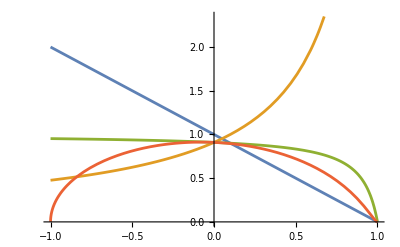

```mathematica
Plot[{1-x, 1/(1-x+0.1),(1-x)/(1-x+0.1),(1-x)Sqrt[1-x^2]/(1-x+0.1)},{x,-1,1}]
```